40

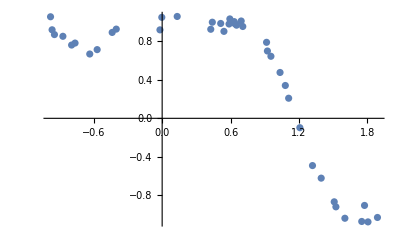

```mathematica
data={{1.603414364747091,-1.0393986596239269},{0.44016418168876625,0.9995843914334753},{1.5098511048519505,-0.8683582353578478},{-0.40277767373925266,0.9277979499107516},{1.3955103337973425,-0.6221594074540295},{1.0807415137899525,0.3414316561956332},{0.5868801894822449,0.9808910295635275},{1.1099604048237928,0.20901841843885618},{-0.019302113445713198,0.919978886086271},{1.7513003227640178,-1.0727311504467838},{0.6378124769271549,0.9844363189004806},{-0.9657772031206847,0.9206806882277448},{1.0343981121800638,0.4768085819653538},{0.5940586151905489,1.033830806184055},{1.5245470073281138,-0.9206594766354125},{-0.003163711070198416,1.0502251737781003},{-0.8709633264692289,0.8530485115958606},{0.9160947751398494,0.7904240787658582},{0.5421564840485265,0.9043359769619412},{1.8061343703160566,-1.0772420426916607},{-0.43854140250576046,0.893191736306055},{-0.9451659524479609,0.8709557637355331},{0.9236461205670847,0.7000471623880626},{-0.9793887493272762,1.0562189944154796},{1.8892480083870207,-1.0311912582494478},{0.4265526354821749,0.9262226917842102},{-0.6352989989410931,0.6688818297512328},{-0.5702836534476268,0.714419739067903},{-0.7643356724718642,0.7826998118567255},{0.5136215714125241,0.9865717935058365},{0.6935078434796096,1.0121318220111148},{0.7074872010964675,0.9551086851857303},{0.1320492459853697,1.0593836411237412},{0.6526531535444282,0.9685874089883433},{1.2084031254182852,-0.09743408772542865},{0.6320419028717041,1.0056023652434747},{1.3191551170312645,-0.49142956412666405},{-0.7945107326104706,0.762030893773024},{0.9544541159723576,0.6451765367480032},{1.7757729208371562,-0.9060891105868454}};
Length[data]
list=ListPlot[data]
```

函数及其图像如下：

Piecewise[{{0.858044+0.161927 Cos[4.55724-7.3189 x], x<-0.235822}, {1.01997, -0.235822≤x≤0.597243}, {-0.0288189+1.04879 Cos[2.67979 (-0.597243+x)], x>0.597243}, {0, True}}]

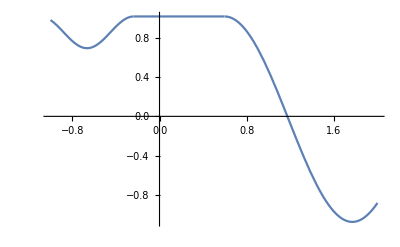

```mathematica
b=7.318904849964189;
c=-4.5572350158394785;
e=-0.23582156301661905;
f=0.5972425483179338;
g=1.0487902872865906;
(*预拟合的结果*)
model=Piecewise[{{a*Cos[b*x+c]+d,x<e},{a*Cos[b*e+c]+d,e≤x≤f},{g*Cos[(x-f)*h]+a*Cos[b*e+c]+d-g,x>f}}];(*定义模型*)
limitation={};
para={a,d,h};(*定义参数*)
approx=FindFit[data,{model,limitation},para,x];
Print["函数及其图像如下："]
params=model/.approx
approxpic=Plot[params,{x,-1,2}]
```

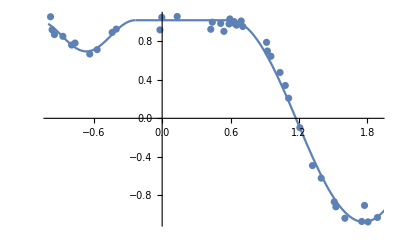

0.996745

```mathematica
Show[list,approxpic]
result=Table[params/.x->data[[i,1]],{i,40}];
Correlation[result,data[[All,2]]](*计算相关性，判断拟合结果*)
```